```mathematica
EulerPred[func_, vars0_, h_, n_]:=(
Res = List[vars0];
Do[Res = Append[Res, Prepend[Table[Res[[i-1, v]]+h *func[[v-1]]@@Res[[i-1]], {v, 2, Length[vars0]}], Res[[i-1,1]]+h]],
{i, 2, n+1}];
Return[Table[Table[{Res[[i, 1]], Res[[i, v]]},{i, 1, n+1}],{v, 2, Length[vars0]}]]);
EulerCorr[f_,A_]:=(
h=Res[[2,1]]-Res[[1,1]];
Do[Res[[i, 2]]=Res[[i-1,2]]+h/2(f@@Res[[i-1]]+f@@Res[[i]]),
{i, 2, Length[A]}];
Return[Res]);
RungeCutta[func_, vars0_, h_, n_]:=(
nv=Length[vars0];
Res = List[vars0];
Do[
Kcoef = List[Prepend[Table[h *func[[v-1]]@@Res[[i-1]],{v, 2, nv}],h]];
Kcoef =Append[Kcoef, Prepend[Table[h *func[[v-1]]@@(Res[[i-1]]+Kcoef[[1]]/2),{v, 2, nv}],h]];
Kcoef =Append[Kcoef, Prepend[Table[h *func[[v-1]]@@(Res[[i-1]]+Kcoef[[2]]/2),{v, 2, nv}],h]];
Kcoef =Append[Kcoef, Prepend[Table[h *func[[v-1]]@@(Res[[i-1]]+Kcoef[[3]]),{v, 2, nv}],h]];
Res = Append[Res, Prepend[Table[Res[[i-1, v]]+1/6(Kcoef[[1,v]]+2 Kcoef[[2,v]]+2 Kcoef[[3,v]]+Kcoef[[4,v]]), {v, 2, Length[vars0]}], Res[[i-1,1]]+h]],
{i, 2, n+1}];
Return[Table[Table[{Res[[i, 1]], Res[[i, v]]},{i, 1, n+1}],{v, 2, nv}]]
);
AbsDelta[f_, A_, n_]:=(Return[Norm[Table[Abs[f[A[[i, 1]]]-A[[i,2]]], {i, 1, n+1}], Infinity]])
```

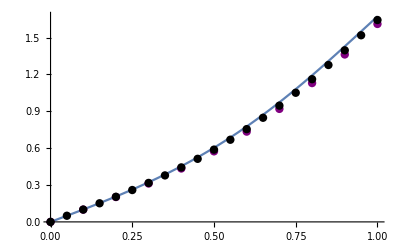

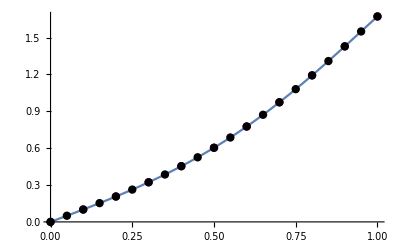

Таблица абсолютных погрешностей

Эйлер-Коши(шаг h=0.10): 0.0659876

Эйлер-Коши(шаг h=0.05): 0.0320388

Рунге-Кутт(шаг h=0.10): 7.88865×10^-6

Рунге-Кутт(шаг h=0.05): 6.417×10^-7

```mathematica
f[x_, y_]:=1 +4 y Sin[x] -1.5 y^2; x0 =0; y0=0;
sol11 =EulerPred[{f}, {x0,y0}, 0.1, (1-0)/0.1];
sol11 = EulerCorr[f, sol11];
sol12=EulerPred[{f}, {x0,y0}, 0.05, (1-0)/0.05];
sol12 = EulerCorr[f, sol12];
sol13=RungeCutta[{f}, {x0,y0}, 0.1, (1-0)/0.1][[1]];
sol14=RungeCutta[{f}, {x0,y0}, 0.05, (1-0)/0.05][[1]];
Clear[sol1,sol1N];
(*sol1 = DSolve[{y'[x]==f[x, y[x]], y[x0]==y0}, y[x], x];
y11[x_]=y[x]/.Flatten[sol1];*)
sol1N = NDSolve[{y'[x]==f[x, y[x]], y[x0]==y0}, y[x], {x, 0, 1}];
y12[x_]=y[x]/.Flatten[sol1N];
Print[Plot[y12[x], {x, 0, 1}, Epilog->{Purple,PointSize[0.015], Point[sol11], Black,PointSize[0.015],Point[sol12]}]];

Print[Plot[y12[x], {x, 0, 1}, Epilog->{Purple,PointSize[0.015], Point[sol13], Black,PointSize[0.015],Point[sol14]}]];
Print["Таблица абсолютных погрешностей"];
Print["Эйлер-Коши","(шаг h=0.10): ",AbsDelta[y12, sol11,(1-0)/0.1 ]]
Print["Эйлер-Коши","(шаг h=0.05): ",AbsDelta[y12, sol12,(1-0)/0.05 ]]
Print["Рунге-Кутт","(шаг h=0.10): ",AbsDelta[y12, sol13,(1-0)/0.1 ]]
Print["Рунге-Кутт","(шаг h=0.05): ",AbsDelta[y12, sol14,(1-0)/0.05 ]]
```

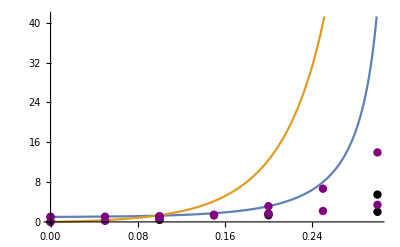

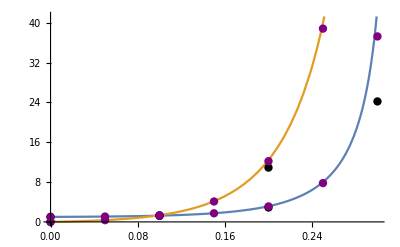

Таблица абсолютных погрешностей

Эйлер-Коши(шаг h=0.10): 207.44

Эйлер-Коши(шаг h=0.05): 198.972

Рунге-Кутт(шаг h=0.10): 89.112

Рунге-Кутт(шаг h=0.05): 26.8043

```mathematica
f2[x_, y_, z_]:=y^2+3z;
g2[x_, y_, z_]:=4(y^2+3z)+7z;
 x0 = 0; y0 = 1; z0 =0; a =0; b =0.3;
Sol21 =EulerPred[{f2,g2}, {x0, y0, z0}, 0.1, (b-a)/0.1];
Sol2y1= Sol21[[1]];
Sol2z1 =Sol21[[2]];
Sol22 = EulerPred[{f2,g2}, {x0, y0, z0}, 0.05, (b-a)/0.05];
sol2y2 = Sol22[[1]];
sol2z2 = Sol22[[2]];

Sol23 =RungeCutta[{f2,g2}, {x0, y0, z0}, 0.1, (b-a)/0.1];
Sol2y3= Sol23[[1]];
Sol2z3=Sol23[[2]];
Sol24 = RungeCutta[{f2,g2}, {x0, y0, z0}, 0.05, (b-a)/0.05];
sol2y4 = Sol24[[1]];
sol2z4 = Sol24[[2]];

Sol2=NDSolve[{y'[x]==f2[x,y[x], z[x]], z'[x]==g2[x,y[x], z[x]], y[x0]==y0, z[x0]==z0}, {y[x], z[x]}, {x, a,b}];
y21[x_]=y[x]/.Flatten[Sol2];
z21[x_]=z[x]/.Flatten[Sol2];
Print[Plot[ {y21[x],z21[x]}, {x, a, b}, Epilog->{Black,PointSize[0.015], Point[Sol2y1],Point[Sol2z1], Purple,PointSize[0.015], Point[sol2y2], Point[sol2z2]}]];

Print[Plot[ {y21[x],z21[x]}, {x, a, b}, Epilog->{Black,PointSize[0.015], Point[Sol2y3],Point[Sol2z3], Purple,PointSize[0.015], Point[sol2y4], Point[sol2z4]}]];

Print["Таблица абсолютных погрешностей"];
Print["Эйлер-Коши","(шаг h=0.10): ",Norm[{AbsDelta[y21, Sol2y1,(b-a)/0.1 ], AbsDelta[z21, Sol2z1,(b-a)/0.1 ]}, Infinity]]
Print["Эйлер-Коши","(шаг h=0.05): ",Norm[{AbsDelta[y21, sol2y2,(b-a)/0.05 ], AbsDelta[z21, sol2z2,(b-a)/0.05 ]}, Infinity]]
Print["Рунге-Кутт","(шаг h=0.10): ",Norm[{AbsDelta[y21, Sol2y3,(b-a)/0.1 ], AbsDelta[z21, Sol2z3,(b-a)/0.1 ]}, Infinity]]
Print["Рунге-Кутт","(шаг h=0.05): ",Norm[{AbsDelta[y21, sol2y4,(b-a)/0.05], AbsDelta[z21, sol2z4,(b-a)/0.05 ]}, Infinity]]
```